```mathematica
Integrate[-pot'[x]Exp[-I j x/L],{x,-L π,L π}]/(2 π L)
```

-(2 ⅈ L (j π (-6 L^2+j^2 (-4+L^2 π^2)) Cos[j π]+(6 L^2+j^2 (4-3 L^2 π^2)) Sin[j π]))/(5 j^4 π)

```mathematica
FullSimplify[%,Assumptions->{j∈Integers}]
```

-(2 ⅈ (-1)^j L (-6 L^2+j^2 (-4+L^2 π^2)))/(5 j^3)

```mathematica
Limit[%,j->0]
```

0

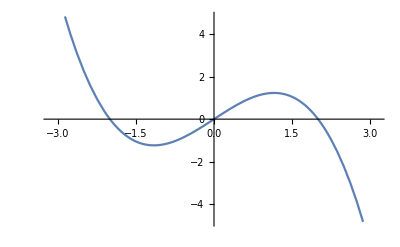

```mathematica
Plot[-pot'[x],{x,-π,π}]
```

```mathematica
-pot'[x]
```

-2/5 x (-4+x^2)

```mathematica
Integrate[pot[x]Exp[-I j x/L],{x,-L π,L π}]/(2 π L)
```

(4 j L^2 π (-6 L^2+j^2 (-4+L^2 π^2)) Cos[j π]+(24 L^4+4 j^2 L^2 (4-3 L^2 π^2)+j^4 (-4+L^2 π^2)^2) Sin[j π])/(10 j^5 π)

```mathematica
FullSimplify[%,Assumptions->{j∈Integers}]
```

(2 (-1)^j L^2 (-6 L^2+j^2 (-4+L^2 π^2)))/(5 j^4)

```mathematica
Limit[%,j->0]
```

8/5-(4 L^2 π^2)/15+(L^4 π^4)/50